```mathematica
ClearAll["Global`*"]
```

```mathematica
(* For the prereheting scenario with inflaton potential , 
we study the Broad and Narrow resonance regime *)
```

```mathematica
mϕ=1.0;                      (* inflation mass *)
tMax=50.0;               (* Time *)
```

## Solve:

```mathematica
A[k_,q_] := k^2/mϕ^2+2q;

ω[z_,k_,q_]:=Sqrt[A[k,q]-2*q*Cos[2*z]];

(* EOM daughter χ *)
eqnχ=χ''[z]+(A[k,q]-2*q*Cos[2*z])*χ[z]==0;

(*Initial conditions*)
χconditions={χ[0]==1/(√(2ω[0,k,q])),χ'[0]==-I*√(ω[0,k,q]/2)}; (* Initial conditions  to be valued at  *)

(*Solve χ dynamic *)
solχ=ParametricNDSolveValue[{eqnχ,χconditions[[1]],χconditions[[2]]},χ,{z,0,tMax},{k,q},MaxSteps->Infinity,Method->"StiffnessSwitching"];
```

# Narrow resonance

```mathematica
(* For  we are in the narrow resonance regime. The resonance occurs only in some narrow bands near  with . The width of each band is of order  . The most relavant band is thus the first one, for which  *)

(* Hence, we expect the resonance peak in the first band for modes  *)
(* The modes in the centre of the resonance  grow as *)
```

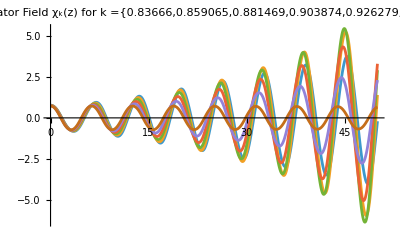

```mathematica
qvalue = 0.1;
AUp =1+ qvalue;
ABelow =1 - qvalue;

kUp = √(mϕ^2(AUp - 2*qvalue));
kBelow = √(mϕ^2(ABelow - 2*qvalue));
kvalues= Range[kBelow, kUp, (kUp - kBelow)/5];
Plot[Evaluate[Table[Re[solχ[k,qvalue][z]],{k,kBelow, kUp, (kUp - kBelow)/5}]],{z,0,tMax},PlotRange->All,PlotLabel->Style[StringForm["Spectator Field χ_k(z) for k =``",kvalues],14]]
```

```mathematica
Manipulate[Plot[Re[solχ[k,qvalue][z]],{z,0,tMax},PlotRange->All,AxesLabel->Automatic,PlotStyle->{Thick,Darker[Blue]},PlotLabel->Style[StringForm["Spectator Field χ_k(z) for k =``",k],14]],{k,kBelow, kUp}]
```

Plot::plln: Limiting value tMax in {z,0,tMax} is not a machine-sized real number.

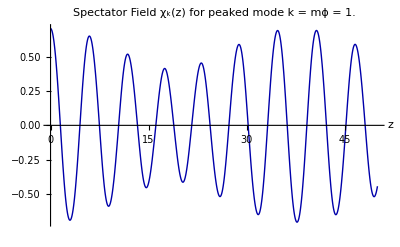

```mathematica
χNarrowPeak = solχ[mϕ,qvalue];
Plot[Re[χNarrowPeak[z]],{z,0,tMax},AxesLabel->Automatic,PlotStyle->{Thick,Darker[Blue]},PlotLabel->Style[StringForm["Spectator Field χ_k(z) for peaked mode k = mϕ = ``",mϕ],14]]
```

## Stability/Instability chart

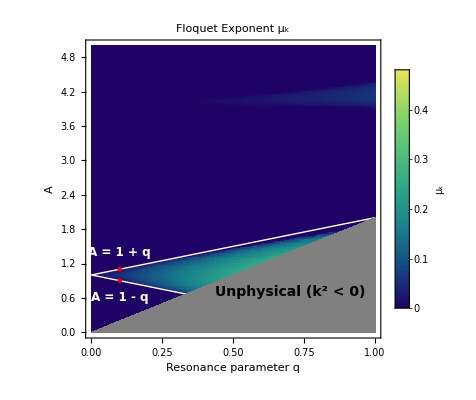

```mathematica
qMaxChart=1;
AMaxChart=5;
μ[A_,q_]:=Abs[Im[MathieuCharacteristicExponent[A,q]]];

plotFloquet=DensityPlot[μ[A,q],{q,0,qMaxChart},{A,0,AMaxChart},PlotPoints->80,MaxRecursion->2,ColorFunction->"BlueGreenYellow",PlotRange->All,PlotLegends->BarLegend[Automatic,LegendLabel->"μ_k"],FrameLabel->{"Resonance parameter q","A"},PlotLabel->"Floquet Exponent μ_k"];
unphysicalRegion=RegionPlot[A<2*q,{q,0,qMaxChart},{A,0,AMaxChart},BoundaryStyle->None,PlotStyle->Directive[Gray,Opacity[1.]]];

Aupper[q_]:=1+q;
Abelow[q_]:=1-q;
plotAqLines=Plot[{Aupper[q],Abelow[q]},{q,0,qMaxChart},PlotStyle->{Directive[Thick,White],Directive[Thick,White]}];

regionPeakUP = ListPlot[{{qvalue,AUp}},PlotStyle->{Red,PointSize[Large]}];
regionPeakBelow = ListPlot[{{qvalue,ABelow}},PlotStyle->{Red,PointSize[Large]}];

Show[plotFloquet,plotAqLines,regionPeakUP,regionPeakBelow,unphysicalRegion,Epilog->{Text[Style["Unphysical (k^2 < 0)",Black,Bold,14],{qMaxChart*0.7,qMaxChart*0.7}],Text[Style["A = 1 + q",White,Bold,12],{qMaxChart*0.1,Aupper[qMaxChart*0.4]}],Text[Style["A = 1 - q",White,Bold,12],{qMaxChart*0.1,Abelow[qMaxChart*0.4]}]}]
```

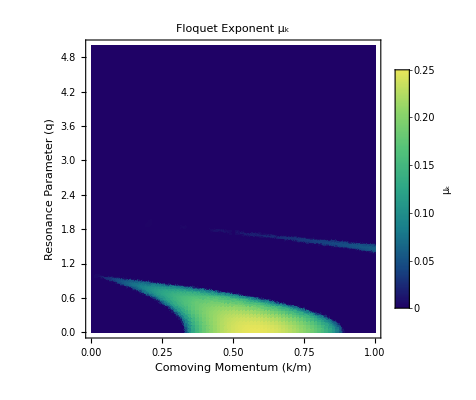

```mathematica
qMaxChart=1;
kMaxChart=5;
μ[k_,q_]:=Abs[Im[MathieuCharacteristicExponent[k^2/mϕ^2+2q,q]]];

plotFloquet=DensityPlot[μ[k,q],{q,0,qMaxChart},{k,0,kMaxChart},PlotPoints->80,MaxRecursion->2,ColorFunction->"BlueGreenYellow",PlotRange->All,PlotLegends->BarLegend[Automatic,LegendLabel->"μ_k"],FrameLabel->{"Comoving Momentum (k/m)","Resonance Parameter (q)"},PlotLabel->"Floquet Exponent μ_k"]
(*unphysicalRegion=RegionPlot[A<2*q,{q,0,qMaxChart},{k,0,kMaxChart},BoundaryStyle->None,PlotStyle->Directive[Gray,Opacity[1.]]];

Aupper[q_]:=1+q;
Abelow[q_]:=1-q;
plotAqLines=Plot[{Aupper[q],Abelow[q]},{q,0,qMaxChart},PlotStyle->{Directive[Thick,White],Directive[Thick,White]}];

regionPeakUP = ListPlot[{{qvalue,AUp}},PlotStyle->{Red,PointSize[Large]}];
regionPeakBelow = ListPlot[{{qvalue,ABelow}},PlotStyle->{Red,PointSize[Large]}];

Show[plotFloquet,plotAqLines,regionPeakUP,regionPeakBelow,unphysicalRegion,Epilog->{Text[Style["Unphysical (k^2 < 0)",Black,Bold,14],{qMaxChart*0.7,qMaxChart*0.7}],Text[Style["A = 1 + q",White,Bold,12],{qMaxChart*0.1,Aupper[qMaxChart*0.4]}],Text[Style["A = 1 - q",White,Bold,12],{qMaxChart*0.1,Abelow[qMaxChart*0.4]}]}]*)
```

# Broad resonance

```mathematica
(* For  (or equivalently large amplitude oscillations), the resonance occurs for modes  (above the line  in the stability/instability chart) *)
```

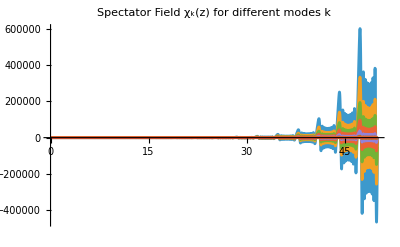

```mathematica
qvalue = 200;
Plot[Evaluate[Table[Re[solχ[k,qvalue][z]],{k,0.2,3.0, (3.0-0.2)/10}]],{z,0,tMax},PlotRange->All,PlotLabel->Style[StringForm["Spectator Field χ_k(z) for different modes k"],14]]
```

```mathematica
Manipulate[Plot[Re[solχ[k,qvalue][z]],{z,0,tMax},PlotRange->All,AxesLabel->Automatic,PlotStyle->{Thick,Darker[Blue]},PlotLabel->Style[StringForm["Spectator Field χ_k(z) for k =``",k],14]],{k,0.2, 3.0}]
```

Plot::plln: Limiting value tMax in {z,0,tMax} is not a machine-sized real number.

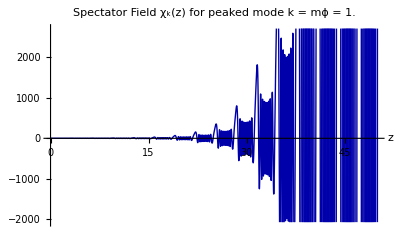

```mathematica
χNarrowPeak = solχ[mϕ,qvalue];
Plot[Re[χNarrowPeak[z]],{z,0,tMax},AxesLabel->Automatic,PlotStyle->{Thick,Darker[Blue]},PlotLabel->Style[StringForm["Spectator Field χ_k(z) for peaked mode k = mϕ = ``",mϕ],14]]
```

## Stability/Instability chart

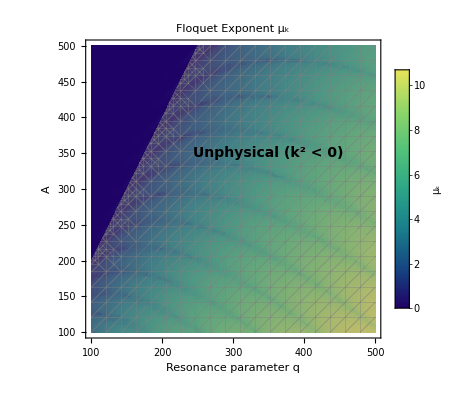

```mathematica
qMaxChart=500;
AMaxChart=500;

plotFloquet=DensityPlot[μ[A,q],{q,100,qMaxChart},{A,100,AMaxChart},PlotPoints->80,MaxRecursion->2,ColorFunction->"BlueGreenYellow",PlotRange->All,PlotLegends->BarLegend[Automatic,LegendLabel->"μ_k"],FrameLabel->{"Resonance parameter q","A"},PlotLabel->"Floquet Exponent μ_k"];
unphysicalRegion=RegionPlot[A<2*q,{q,100,qMaxChart},{A,100,AMaxChart},BoundaryStyle->None,PlotStyle->Directive[Gray,Opacity[0.4]]];

Show[plotFloquet,unphysicalRegion,Epilog->{Text[Style["Unphysical (k^2 < 0)",Black,Bold,14],{qMaxChart*0.7,qMaxChart*0.7}]}]
```